### PARAMETRES

```mathematica
ClearAll;
listH ={10,1,10}; (*мощности слоев*)
slopes = {0Degree,-0.4Degree,0.3Degree,-0.5Degree} ;(*наклон слоев*)
len = 1000;(*длина профиля*)
dx = 10;(*шаг по профилю*)
hDispersion = 50;(*степень складчатости нижнего слоя в метрах*)
hTapering =2 ; (*степень влияния нижнего горизонта на верхние*)
listV = {2700,2500,3000, 3500}; (*набор скоростей*)
wellCount= 10 ;(*кол скважин*)
wellType = "regular"; (*расположение скважин "max","min","regular","random"*)
type = -1 ;(*выполаживание. 1 - кверху, -1 - книзу*)
velocityTrend = 1;(*1 or 0*)
velocityAnomaly =0; (*1 or 0*)(*1 or 0*)
```

### DEPTH

```mathematica
horizons = BuildDepthSection[listH,slopes,len,dx,hDispersion,hTapering, type][["horizons"]];
table = BuildDepthSection[listH,slopes,len,dx,hDispersion,hTapering, type][["table"]];
optsDepth = {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Depth Section"};
PlotDepthSection[horizons, optsDepth]
```

-Graphics-

### VELOCITY

```mathematica
velModel=BuildVelocitySection[horizons,listV, velocityTrend, velocityAnomaly][["model"]];
datasetVelModel=BuildVelocitySection[horizons,listV, velocityTrend, velocityAnomaly][["dataset"]];
optsVel1 = {PlotStyle -> {Directive[Thickness[0.005], Black]},
							PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
							ImageSize -> 500};
optsVel2 = {ColorFunction -> ColorData[{"RedBlueTones", "Reverse"}],
						PlotLegends -> BarLegend[Automatic, LegendLabel -> "Vel, m/s"],
						PlotLabel -> "Velocity Distribution",
						Contours -> {Automatic, 20},
					GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None}};
PlotVelocity[velModel, horizons,{optsVel1, optsVel2}]
```

-Graphics-

### TIME

```mathematica
time=BuildTimeSection[horizons, velModel][["time"]];
optsTime = {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[time]] - 1)],
						PlotLabel -> "Time Section"};
PlotTimeSection[time, optsTime]
```

-Graphics-

### WELLS

```mathematica
wellDataset = BuildWellSet[horizons, time, wellCount, wellType][["dataset"]];
positions = BuildWellSet[horizons, time,  wellCount, wellType][["positions"]];
PlotDepthSection[horizons, {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Depth Section",GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},											
											PlotLabel -> "Depth Section with wells"}]
```

-Graphics-

```mathematica
PlotTimeSection[time, {GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
					    Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[time]] - 1)],
						PlotLabel -> "Time Section with Wells"
}]
```

-Graphics-

### CheckVelocity

```mathematica
datasetVint= CheckVelocity[wellDataset][["dataset"]]
```

### HTMethod

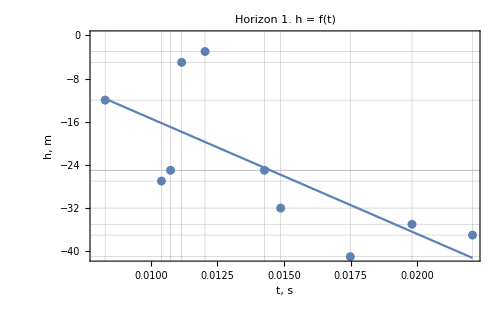
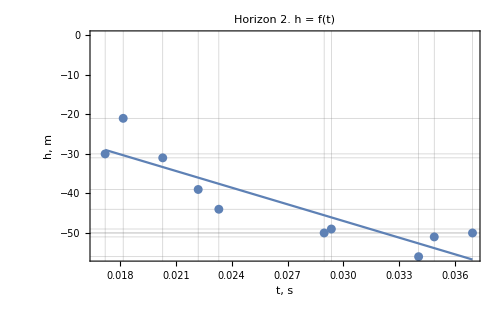
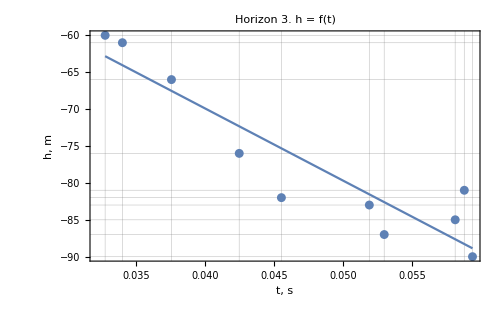

```mathematica
Clear[t];
lmSetHT=HTMethod[wellDataset,time, t][["lmSet"]];
lmParametresHT=HTMethod[wellDataset, time, t][["lmParametres"]];
resultHT=HTMethod[wellDataset, time, t][["result"]];
wellValuesHT=HTMethod[wellDataset, time, t][["wellValues"]];
PlotHT[wellValuesHT,lmSetHT, t]
```

### VTMethod

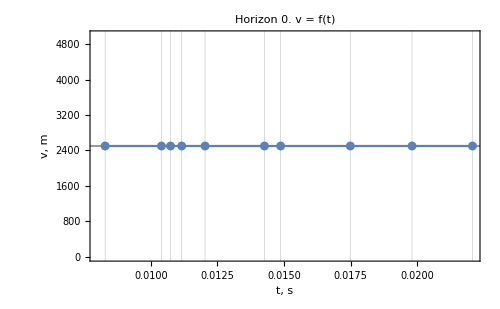
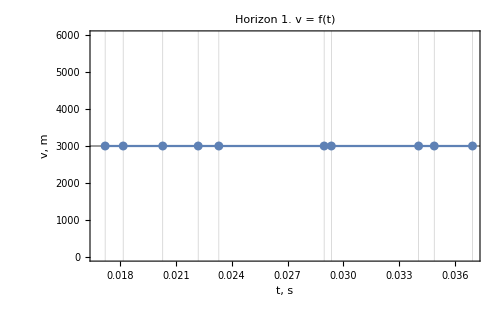
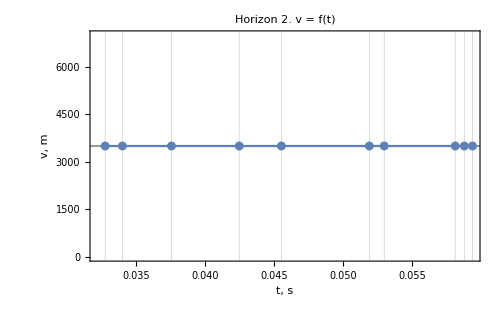

```mathematica
lmSetVT=VTMethod[wellDataset,datasetVelModel,time, t][["lmSet"]];
lmParametresVT=VTMethod[wellDataset,datasetVelModel,time, t][["lmParametres"]];
wellValuesVT=VTMethod[wellDataset,datasetVelModel,time, t][["wellValues"]];
resultVT = VTMethod[wellDataset,datasetVelModel,time, t][["result"]];
fitsVT = VTMethod[wellDataset,datasetVelModel,time, t][["fits"]];
PlotVT[wellValuesVT,lmSetVT, t]
```

### THMethod

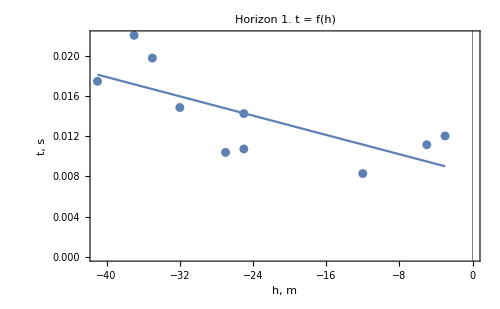
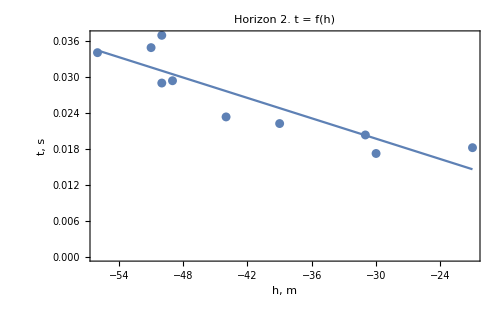
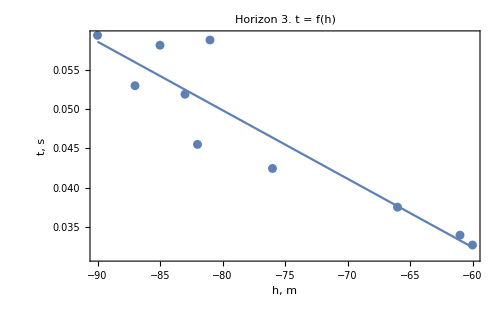

```mathematica
Clear[h];
lmSetTH=THMethod[wellDataset,time, h][["lmSet"]];
lmParametresTH=THMethod[wellDataset, time, h][["lmParametres"]];
wellValuesTH = THMethod[wellDataset, time, h][["wellValues"]];
resultTH=THMethod[wellDataset, time, h][["result"]];
PlotTH[wellValuesTH,lmSetTH, h]
```

### VaveMethod

```mathematica
vAveTable=VaveMethod[wellDataset,time][["vAveTable"]];
resultVave=VaveMethod[wellDataset, time][["result"]];
fitsVave = VaveMethod[wellDataset, time][["fits"]]
```

{{{0,-28.7527},{10,-27.4672},{20,-25.5448},{30,-21.6303},{40,-20.1748},{50,-17.9389},{60,-16.183},{70,-13.2393},{80,-13.5217},{90,-17.111},{100,-18.3394},{110,-17.8373},{120,-17.2149},{130,-17.5773},{140,-18.004},{150,-17.2472},{160,-18.2257},{170,-17.5034},{180,-18.5722},{190,-19.5439},{200,-20.1286},{210,-20.221},{220,-19.8481},{230,-19.4333},{240,-17.4312},{250,-19.9136},{260,-24.48},{270,-26.788},{280,-27.8902},{290,-27.3367},{300,-25.6182},{310,-23.4682},{320,-22.989},{330,-24.8867},{340,-29.3103},{350,-36.306},{360,-41.7201},{370,-44.8392},{380,-42.3699},{390,-36.2301},{400,-29.069},{410,-19.792},{420,-23.2148},{430,-24.5255},{440,-23.911},{450,-23.4829},{460,-21.0363},{470,-18.6464},{480,-25.6098},{490,-33.957},{500,-38.9183},{510,-40.1689},{520,-39.5239},{530,-33.3275},{540,-24.9293},{550,-18.9764},{560,-22.8817},{570,-25.8004},{580,-25.7402},{590,-23.2223},{600,-19.7154},{610,-17.8159},{620,-25.3799},{630,-31.3842},{640,-33.1914},{650,-32.5653},{660,-30.807},{670,-26.7716},{680,-23.4682},{690,-23.4029},{700,-23.948},{710,-27.4373},{720,-31.4665},{730,-36.2584},{740,-36.9949},{750,-35.244},{760,-29.1481},{770,-21.448},{780,-13.7082},{790,-17.7409},{800,-20.0431},{810,-21.351},{820,-21.7546},{830,-20.6909},{840,-18.7048},{850,-16.222},{860,-13.15},{870,-11.1464},{880,-10.2031},{890,-10.3481},{900,-10.9139},{910,-10.9108},{920,-11.3925},{930,-12.3783},{940,-13.8915},{950,-15.3123},{960,-15.1554},{970,-15.0542},{980,-14.9623},{990,-14.3507},{1000,-16.642}},{{0,-32.4197},{10,-32.133},{20,-31.7084},{30,-28.9298},{40,-28.957},{50,-28.2471},{60,-27.998},{70,-26.1351},{80,-27.8296},{90,-32.203},{100,-34.3081},{110,-34.2998},{120,-34.1772},{130,-34.9904},{140,-35.3661},{150,-34.6469},{160,-35.5474},{170,-34.861},{180,-35.8479},{190,-36.7713},{200,-37.7936},{210,-37.8523},{220,-37.9936},{230,-38.5645},{240,-37.129},{250,-39.9556},{260,-45.2655},{270,-47.927},{280,-49.949},{290,-49.8918},{300,-49.2377},{310,-47.664},{320,-47.7219},{330,-49.4817},{340,-54.2},{350,-60.8486},{360,-65.48},{370,-68.4442},{380,-65.6279},{390,-59.2817},{400,-51.9672},{410,-42.6825},{420,-45.9745},{430,-46.713},{440,-46.129},{450,-45.7604},{460,-43.4352},{470,-41.1639},{480,-47.8208},{490,-55.7538},{500,-60.469},{510,-61.6973},{520,-61.0843},{530,-54.686},{540,-46.7435},{550,-40.5773},{560,-43.7825},{570,-46.5563},{580,-45.995},{590,-44.1061},{600,-40.7733},{610,-39.4743},{620,-47.1327},{630,-53.3485},{640,-55.5365},{650,-55.4539},{660,-54.2977},{670,-50.9346},{680,-47.7951},{690,-48.2514},{700,-48.8167},{710,-51.6127},{720,-54.9691},{730,-59.095},{740,-58.8045},{750,-56.1947},{760,-49.4167},{770,-40.647},{780,-32.3488},{790,-34.737},{800,-35.9554},{810,-36.2592},{820,-35.6785},{830,-34.1987},{840,-32.3354},{850,-30.0004},{860,-27.106},{870,-25.2018},{880,-24.8297},{890,-24.9676},{900,-25.5328},{910,-25.5298},{920,-26.0157},{930,-26.4507},{940,-27.4151},{950,-28.2916},{960,-27.1718},{970,-26.6028},{980,-25.5494},{990,-24.4771},{1000,-26.1835}},{{0,-57.1364},{10,-57.2979},{20,-57.7815},{30,-55.3552},{40,-56.3212},{50,-56.529},{60,-57.2258},{70,-56.2535},{80,-58.9953},{90,-64.0408},{100,-67.2295},{110,-67.7254},{120,-68.1064},{130,-69.4657},{140,-70.3746},{150,-69.626},{160,-71.0861},{170,-70.3716},{180,-71.9274},{190,-72.8885},{200,-74.4877},{210,-75.0904},{220,-75.2375},{230,-76.3816},{240,-75.4461},{250,-78.9569},{260,-85.0648},{270,-88.4315},{280,-91.1508},{290,-91.7311},{300,-91.7235},{310,-90.8105},{320,-90.8708},{330,-93.5213},{340,-98.432},{350,-105.352},{360,-110.172},{370,-113.257},{380,-109.507},{390,-102.902},{400,-95.2892},{410,-84.901},{420,-87.654},{430,-88.4227},{440,-87.8148},{450,-86.7913},{460,-84.3714},{470,-82.0074},{480,-88.321},{490,-96.5775},{500,-101.485},{510,-102.167},{520,-101.529},{530,-94.8694},{540,-86.0216},{550,-79.604},{560,-82.9399},{570,-85.8268},{580,-85.2427},{590,-83.2767},{600,-79.808},{610,-78.4561},{620,-87.0081},{630,-93.4774},{640,-96.3513},{650,-96.2654},{660,-95.062},{670,-92.1766},{680,-88.909},{690,-89.3839},{700,-89.3575},{710,-92.2675},{720,-95.1641},{730,-98.3078},{740,-97.447},{750,-93.6391},{760,-86.0495},{770,-75.8708},{780,-66.2034},{790,-67.6758},{800,-68.4433},{810,-67.7687},{820,-66.6736},{830,-64.6459},{840,-62.222},{850,-59.3099},{860,-55.818},{870,-53.8362},{880,-52.9722},{890,-53.1157},{900,-53.2295},{910,-53.2264},{920,-53.26},{930,-53.7127},{940,-54.2465},{950,-54.691},{960,-53.0599},{970,-52.004},{980,-50.4459},{990,-49.3299},{1000,-50.6459}}}

### GRAPHICS

```mathematica
Show[ListLinePlot[horizons, GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 1000,
					PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)], PlotStyle->Gray],
	ListLinePlot[resultHT[[2;;-1]], PlotStyle->{Blue}],
	ListLinePlot[resultVT[[2;;-1]] , PlotStyle->{Orange}],
	ListLinePlot[resultTH[[2;;-1]], PlotStyle->{Green}],
ListLinePlot[resultVave[[2;;-1]], PlotStyle->{Red}]
]
```

-Graphics-

```mathematica
PlotDepthSection[resultHT,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "H(t)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVT ,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "V(t)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultTH,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "T(H)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVave,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Vave"]
```

-Graphics-